# “Semi-Inclusive Deep Inelastic Scattering in Wandzura-Wilczek-type approximation” S. Bastami, H. Avakian, A. V. Efremov, A. Kotzinian, B. U. Musch, B. Parsamyan, A. Prokudin, M. Schlegel, G. Schnell, P. Schweitzer, K. Tezgin, W. Vogelsang author : Alexei Prokudin, Kemal Tezgin email : prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/WW-SIDIS

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1.01 (06/05/2018)

e-mail: prokudin@jlab.org, kemal.tezgin@uconn.edu

https://github.com/prokudin/WW-SIDIS

If you use this package, please, site Bastami:2018xqd for this paper and https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

Contains the following constants:

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

Unpolarized parton distribution functions:

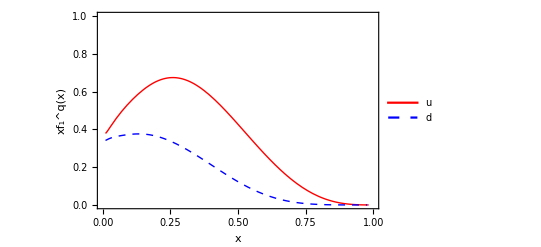

RGBColor[1, 0, 0]If you use these functions, please, cite bibitem{Martin:2009iq}RGBColor[1, 0, 0]

```mathematica
Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
Print[Red,"If you use these functions, please, cite bibitem{Martin:2009iq}",Red]
```

Sivers parton distribution functions:

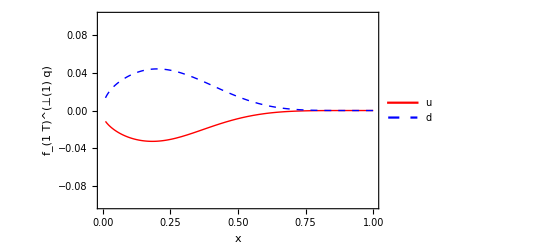

RGBColor[1, 0, 0]If you use these functions, please, cite bibitem{Anselmino:2011gs}RGBColor[1, 0, 0]

```mathematica
Plot[{x f1TperpuFirstMoment[x,2.4],x f1TperpdFirstMoment[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","f_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"},{0.7,0.7}]]
Print[Red,"If you use these functions, please, cite bibitem{Anselmino:2011gs}",Red]
```

Sivers asymmetry:

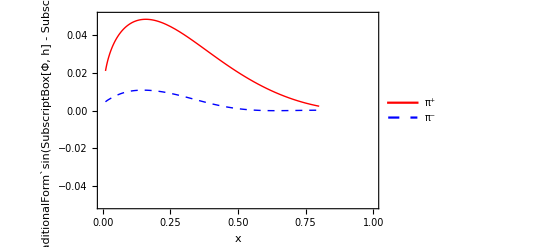

```mathematica
xbj = 0.3; (*x Bjorken*)
zh = 0.3; (*z hadron*)
Q2 = 2.4; (*Q2*)
pT = 0.5; (* hadron transverse momentum *)
Plot[{AUTSivers["pi+",x,zh,Q2, pT],AUTSivers["pi-",x,zh,Q2, pT]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```

Cross section of SIDIS as function of ϕ_has in Eq. (2.3):

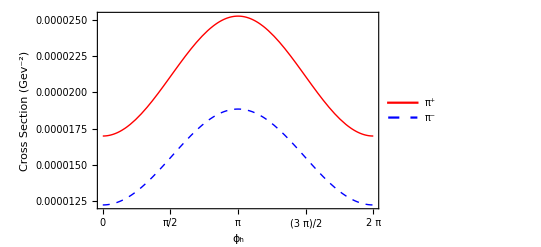

./figs/cross_section_phih.pdf

```mathematica
xbj = 0.3; (*x Bjorken*)
zh = 0.2; (*z hadron*)
Q2 = 2.4; (*Q2*)
pT = 0.5; (* hadron transverse momentum *)
Energy = 5.7; (*Beam energy*)
helicity = 0; (*Beam helicity lambda: Type -1,0,1 for helicity=-1,0,1 respectively *)
polarization = "T"; (*Target polarization: Type "U","L","T" for unpolarized,longitudinally,transversely polarized target resp.*)
phiS = Pi/2; (*Polarization angle*)

xticks = {0,Pi/2,Pi,3/2Pi, 2Pi};

 Plot[{CrossSection["pi+",xbj,zh,Q2,pT,Energy,phih,phiS,helicity,polarization],CrossSection["pi-",xbj,zh,Q2,pT,Energy,phih,phiS,helicity,polarization]},{phih,0,2 Pi},
Frame-> True,
FrameStyle->Directive[Black],
FrameTicks-> {{Automatic,None},{xticks,None}},
FrameTicksStyle->Black,
PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}},
PlotRange->{{0,2 Pi},Automatic},
FrameLabel->{"ϕ_h","Cross Section (Gev^-2)"},
BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.85}]]



Export["./figs/cross_section_phih.pdf",%]
```

Cross section of SIDIS as function of ϕ_Sas in Eq. (2.3):

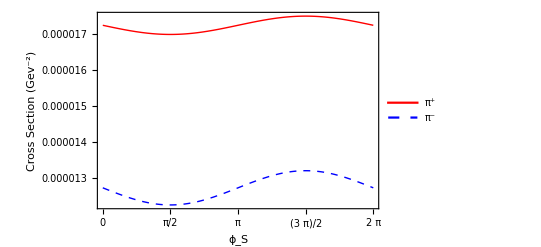

./figs/cross_section_phiS.pdf

```mathematica
xbj = 0.3; (*x Bjorken*)
zh = 0.2; (*z hadron*)
Q2 = 2.4; (*Q2*)
pT = 0.5; (* hadron transverse momentum *)
Energy = 5.7; (*Beam energy*)
helicity = 0; (*Beam helicity lambda: Type -1,0,1 for helicity=-1,0,1 respectively *)
polarization = "T"; (*Target polarization: Type "U","L","T" for unpolarized,longitudinally,transversely polarized target resp.*)
phih = 0; (*Hadron angle*)

xticks = {0,Pi/2,Pi,3/2Pi, 2Pi};


Plot[{CrossSection["pi+",xbj,zh,Q2,pT,Energy,phih,phiS,helicity,polarization],CrossSection["pi-",xbj,zh,Q2,pT,Energy,phih,phiS,helicity,polarization]},{phiS,0,2 Pi},
Frame-> True,
FrameStyle->Directive[Black],
FrameTicks-> {{Automatic,None},{xticks,None}},
FrameTicksStyle->Black,
PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}},
PlotRange->{{0,2 Pi},All},
FrameLabel->{"ϕ_S","Cross Section (Gev^-2)"},
BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.55}]]



Export["./figs/cross_section_phiS.pdf",%]
```

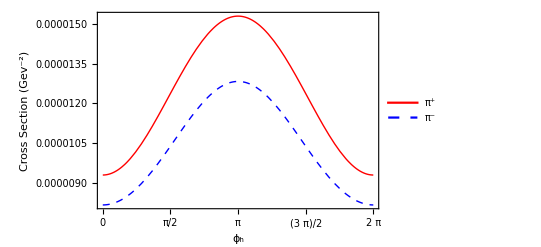

```mathematica
xbj = 0.3; (*x Bjorken*)
zh = 0.2; (*z hadron*)
Q2 = 2.4; (*Q2*)
pT = 0.5; (* hadron transverse momentum *)
Energy = 5.7; (*Beam energy*)
helicity = -1; (*Beam helicity lambda: Type -1,0,1 for helicity=-1,0,1 respectively *)
polarization = "L"; (*Target polarization: Type "U","L","T" for unpolarized,longitudinally,transversely polarized target resp.*)
phiS = Pi/2; (*Polarization angle*)

xticks = {0,Pi/2,Pi,3/2Pi, 2Pi};

 Plot[{CrossSection["pi+",xbj,zh,Q2,pT,Energy,phih,phiS,helicity,polarization],CrossSection["pi-",xbj,zh,Q2,pT,Energy,phih,phiS,helicity,polarization]},{phih,0,2 Pi},
Frame-> True,
FrameStyle->Directive[Black],
FrameTicks-> {{Automatic,None},{xticks,None}},
FrameTicksStyle->Black,
PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}},
PlotRange->{{0,2 Pi},Automatic},
FrameLabel->{"ϕ_h","Cross Section (Gev^-2)"},
BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.85}]]
```